```mathematica
Clear [global]
```

### Constants

```mathematica
h=6.62606896 10^-34;
hbar=h/(2Pi);
kb=1.3806504 10^-23;
c=2.99792458 10^8;
λRb=780.24 10^-9;
uB=9.27400968*10^-24;
Ahfs=h*3.417341305452145 10^9;
gS=2.0023193043622;
gL=0.99999369;
gI=-0.0009951414;
gJ=2.00233113;
(* gJ=gL(J(J+1)-S(S+1)+L(L+1))/(2J(J+1))+gS(J(J+1)+S(S+1)-L(L+1))/(2J(J+1)); *)
gF=gJ(F(F+1)-I'(I'+1)+J(J+1))/(2F(F+1))+gI(F(F+1)+I'(I'+1)-J(J+1))/(2F(F+1));
gF'=gJ*(F'(F'+1)-I1(I1+1)+J(J+1))/(2F'(F'+1))+gI(F'(F'+1)+I1(I1+1)-J(J+1))/(2F'(F'+1));
```

### Breit-Rabi formula (for ground states)

```mathematica
uB 15 10^-3 10^-4 100/(1.44 10^-25)
```

0.00966043

```mathematica
(* s=1/2(gF mF uB B')/mRb t^2 *)
s=1/2(1/2 2 uB 4/10000)/m(0.02)^2
```

(7.41921×10^-31)/m

```mathematica
I'=3/2;
J=1/2;
S=1/2;
L=0;
```

```mathematica
Ehfs[f_]=Ahfs/2(f(f+1)-I'(I'+1)-J(J+1));
ΔEhfs=Ahfs(I'+1/2)
```

4.52871×10^-24

```mathematica
mJ=-1/2;
mI=-1/2;
E1[mj_,mi_,B_]=If[mi+mj==I'+1/2,((ΔEhfs I')/(2I'+1)+1/2(gJ+2gI) uB  B/10000)/(h 10^9),If[mi+mj==-(I'+1/2),((ΔEhfs I')/(2I'+1)-1/2(gJ+2gI) uB  B/10000)/(h 10^9),If[mj==1/2,(-ΔEhfs/(2(2I'+1))+gI uB (mi+mj)B/10000+ΔEhfs/2(1+(4(mi+mj))/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9),(-ΔEhfs/(2(2I'+1))+gI uB (mi+mj)B/10000-ΔEhfs/2(1+(4(mi+mj))/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9)]]];
Manipulate[Plot[{E1[1/2,3/2,B],E1[1/2,1/2,B],E1[1/2,-1/2,B],E1[1/2,-3/2,B],
E1[-1/2,3/2,B],E1[-1/2,1/2,B],E1[- 1/2,-1/2,B],E1[-1/2,-3/2,B]},{B,0,B0}],{{B0,1500},100,3000}]
```

```mathematica
E2[f_,mf_,B_]=If[mf==I'+1/2,((ΔEhfs I')/(2I'+1)+1/2(gJ+3gI) uB  B/10000)/(h 10^9),If[mf==-(I'+1/2),((ΔEhfs I')/(2I'+1)-1/2(gJ+3gI) uB  B/10000)/(h 10^9),If[f==I'+1/2,(-ΔEhfs/(2(2I'+1))+gI uB mf B/10000+ΔEhfs/2(1+(4mf)/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9),(-ΔEhfs/(2(2I'+1))+gI uB mf B/10000-ΔEhfs/2(1+(4mf)/(2I'+1)((gJ-gI)uB B/10000)/ΔEhfs+(((gJ-gI)uB B/10000)/ΔEhfs)^2)^(1/2))/(h 10^9)]]];
Manipulate[Plot[{E2[1,1,B],E2[1,0,B],E2[1,-1,B],E2[2,2,B],
E2[2,1,B],E2[2,0,B],E2[2,-1,B],E2[2,-2,B]},{B,0,B0}],{{B0,1500},100,3000}]
```

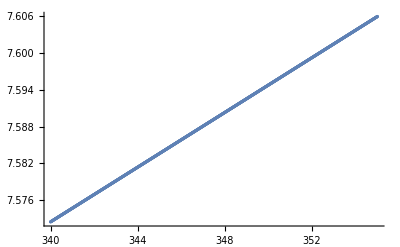

6.81222+0.00223593 x

```mathematica
ListPlot[Table[{B,E2[2,2,B]-E2[1,1,B]},{B,340,355,0.01}]]
Fit[Table[{B,E2[2,2,B]-E2[1,1,B]},{B,340,355,0.01}],{1,x},x]
```

#### Energy difference bewteen F mF and F' mF states in ground states

```mathematica
6834.683203808538
```

```mathematica
6834.683203808538
```

```mathematica
616-220
```

396

```mathematica
B=347.64;
(*Plot[(E2[F,mF,B]-E2[F',mF',B])*1000-6834.679,{B,0,1000}]*)

F=1;
mF=0;
F1=1;
mF'=1;
(*Plot[{E2[2,-1,B]-E2[1,0,B]}*1000,{B,300, 400}]*)

ΔE'=N[(E2[F,mF,B]-E2[F1,mF',B])1000,20 ]   (* Unit in MHz*)
1.10482+3.63496 %
FindRoot[233.562==(Abs[E2[F,mF,Bb]-E2[F1,mF',Bb]])*10^3,{Bb,0.1}]
```

233.843

851.114

{Bb→347.201}

```mathematica
t
```

```mathematica
t
```

```mathematica
-6712.800809589254
```

-6712.8

```mathematica
33.3123 0.912/0.5
```

60.7616

```mathematica
6811.385549138922-6812.054052780136
```

-0.668504

```mathematica
(E2[F,mF,591]-E2[F1,mF',591])*10^3
```

-5677.21

```mathematica
(E2[1,1,B]-E2[1,-1,B])/2 1000
```

-242.325

```mathematica
(E2[1,0,B]-E2[1,-1,B])1000
```

-250.807

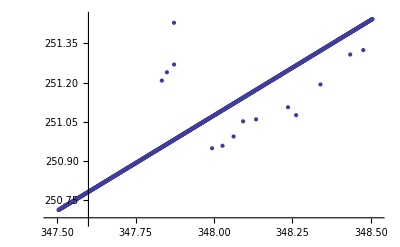

-Graphics-

```mathematica
6868.702188624772
```

6868.7

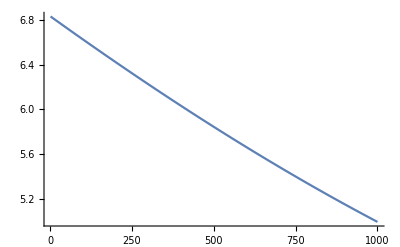

```mathematica
Ed[B2_]=E2[2,-2,B2]-E2[1,-1,B2];
Plot[Ed[B2],{B2,1,1000}]
```

```mathematica
(6 10^-6 mRb)/(uB (23 10^-3)^2)
```

1.223×10^21 mRb

```mathematica
mRb
```

mRb

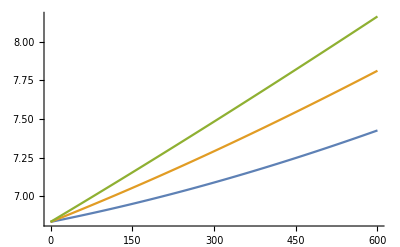

```mathematica
Plot[{E2[2,0,B]-E2[1,1,B],E2[2,1,B]-E2[1,1,B],E2[2,2,B]-E2[1,1,B]},{B,0,600}]
```

```mathematica
(*DAC2*)Br=1.8440*(DAC2-0.08072)/.DAC2->0.08072
(*DAC3*)Ba=0.2129*(DAC3-0.75671)/.DAC3->2
(*DAC15*)Bu=1.1111*(DAC15-0.38063) /.DAC15->0.38063
B=√(Br^2+Ba^2+Bu^2)
```

0.

0.264696

0.

0.264696

```mathematica
(*B=7.22715232;*) (* Unit in Gauss*)

F=1;
mF=-1;
F1=2;
mF'=0;

ΔE'=(E2[F,mF,B]-E2[F1,mF',B])*10^3    (* Unit in MHz*)
h % 10^6/kb 10^6(*Unit in μK*)

NSolve[-6834.48326==(E2[F,mF,Bb]-E2[F1,mF',Bb])*10^3,{Bb}]
```

-6834.5

-328004.

{{Bb→1302.29},{Bb→0.283884}}

```mathematica
232.93012894829877
```

232.93

```mathematica
6652.912707427146-6652.912369570446
```

0.000337857

```mathematica
6652.912369570446-6652.912707427146
```

-0.000337857